fileaddress

Fig3a.pdf

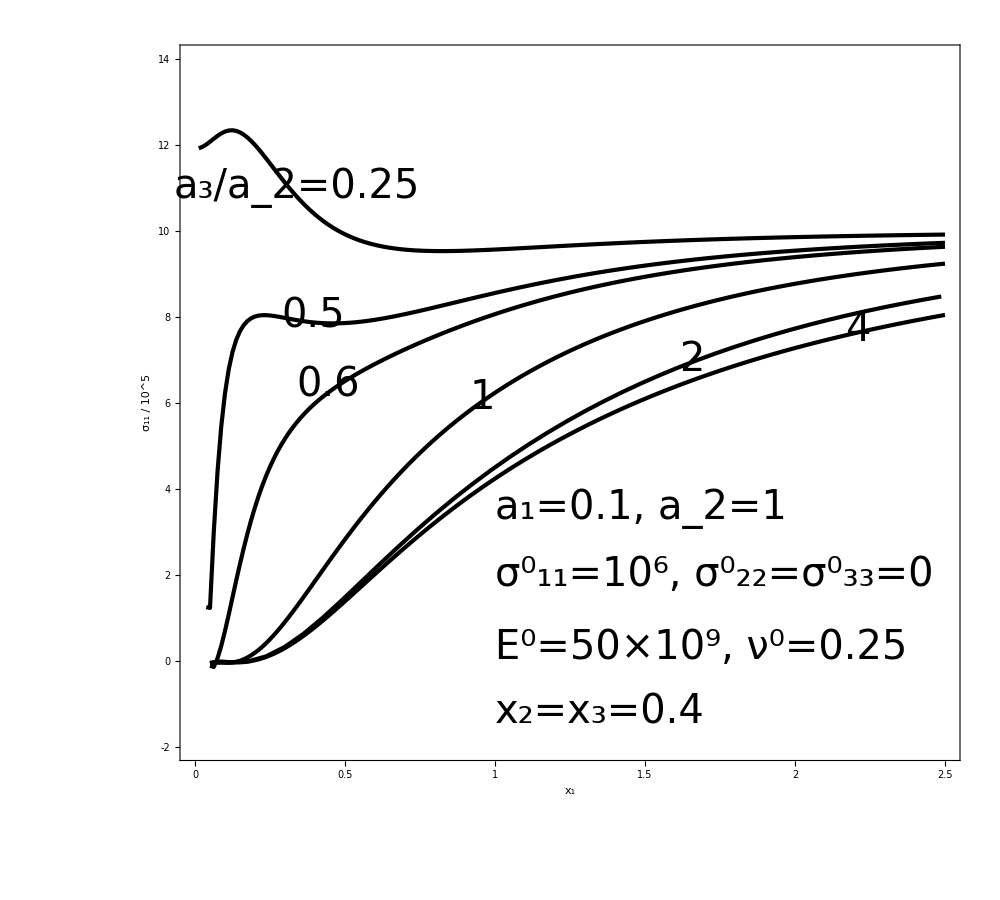

```mathematica
Clear["Global`*"];

(*---------------------------------------------------------------------------------------------------------*)
fileaddress=Directory[]<>"\\plot_style.nb";
NotebookEvaluate[fileaddress(*,InsertResults->True*)];
Print[fileaddress];

(*---------------------------------------------------------------------------------------------------------*)


SetDirectory[NotebookDirectory[]];
Get["plot_style.mx"];
Get["input_report.mx"];



Clear[i];
m[i_]=fr[xp1[i],xp2[i],xp3[i]];
Get["Fig3a4.mx"];
data[4]=Table[{m[k][[1]],m[k][[4]]/10^5},{k,5,howmany+1,1}];(*x[1],σ[33]*)

(*---------------------------*)
Get["Fig3a2.mx"];
data[2]=Table[{m[k][[1]],m[k][[4]]/10^5},{k,5,howmany+1,5}];(*x[1],σ[33]*)

(*---------------------------*)
Get["Fig3a1.mx"];
data[1]=Table[{m[k][[1]],m[k][[4]]/10^5},{k,5,howmany+1,1}];(*x[1],σ[33]*)

(*---------------------------*)
Get["Fig3ap6.mx"];
data[.6]=Table[{m[k][[1]],m[k][[4]]/10^5},{k,5,howmany+1,1}];(*x[1],σ[33]*)

(*---------------------------*)
Get["Fig3ap5.mx"];
data[.5]=Table[{m[k][[1]],m[k][[4]]/10^5},{k,4,howmany+1,1}];(*x[1],σ[33]*)

(*---------------------------*)
Get["Fig3ap25.mx"];
data[.25]=Table[{m[k][[1]],m[k][[4]]/10^5},{k,2,howmany+1,1}];(*x[1],σ[33]*)

(*---------------------------*)





imgSize=1000;

fsmehvarx=40/1000*imgSize; (*font size x axis*)
fsmehvary=40/1000*imgSize ;     (*font size y axis*)

dataseries={data[.25],data[.5],data[.6],data[1],data[2],data[4]};

filetitle=StringReplace[resultfilename,"mx"->"pdf"]



figure=Show[{ListPlot[dataseries
,PlotStyle->{{Black,Bold,Thickness[.003/1000*imgSize]}}
,Joined->{True}

,AxesStyle->Large
,PlotRange->{{0,2.5},{-2,14}}
,GridLines->{None,None}

,AspectRatio->9/10
,LabelStyle->{(*Bold,*)FontSize-> 30/1000*imgSize}
,ImageSize->imgSize


,Frame-> True
,FrameStyle->Directive[Thick,FontSize->1*fsmehvarx]
,FrameTicks->{{{-2,0,2,4,6,8,10,12,14},None},{{0,.5,1,1.5,2,2.5},None}}
(*,FrameTicks->All*)
,FrameLabel->{
{Text[Row[{Style[  "σ_11 / 10^5  ",Italic,fsmehvary]}]],None}
,{Text[Row[{Style["x_1  ",Italic,fsmehvarx](*,Style["Inhomogeneity aspect ratio",fsmehvarx]*)}]],None}}


,Axes->False

]
,Graphics[Text[StyleForm["a_3/a_2=0.25",Italic,1*fsmehvarx,Background->White],{0.75,11},{1,0}]]
,Graphics[Text[StyleForm["0.5",Italic,1*fsmehvarx,Background->White],{.5,8.0},{1,0}]]
,Graphics[Text[StyleForm["0.6",Italic,1*fsmehvarx,Background->White],{.55,6.4},{1,0}]]
,Graphics[Text[StyleForm["1",Italic,1*fsmehvarx,Background->White],{1,6.1},{1,0}]]
,Graphics[Text[StyleForm["2",Italic,1*fsmehvarx,Background->White],{1.7,7},{1,0}]]
,Graphics[Text[StyleForm["4",Italic,1*fsmehvarx,Background->White],{2.25,7.7},{1,0}]]
,Graphics[Text[StyleForm["a_1=0.1, a_2=1  ",Italic,1*fsmehvarx],{1,4},{-1,01}]]
,Graphics[Text[StyleForm["(σ^0)_11=10^6, (σ^0)_22=(σ^0)_33=0  ",Italic,1*fsmehvarx],{1,2},{-1,0}]]
,Graphics[Text[StyleForm["E^0=50×10^9, ν^0=0.25 ",Italic,1*fsmehvarx],{1,.3},{-1,0}]]
,Graphics[Text[StyleForm["x_2=x_3=0.4 ",Italic,1*fsmehvarx],{1,-1.2},{-1,0}]]

}]

Export["Fig3a.pdf",Show[figure]];
```